Plot of the 192 points of domain D

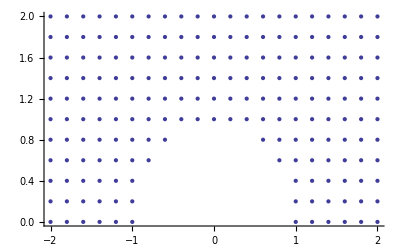

Plot of the gradient vector fields

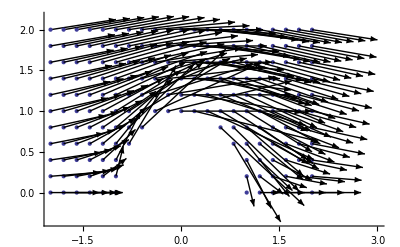

```mathematica
Clear[i,x,y,pList,lPlot,arr]
f[x_,y_]:=x+x/(x^2+y^2);
arr={};
gradf[x_,y_]:=Evaluate[{D[f[x,y],x],D[f[x,y],y]}];
gLine[x_,y_]={x,y}+gradf[x,y];
x=-2.;
pList={};
i=0;
While[x≤2.,
y=0;
While[y≤2.,
	If[x^2+y^2≥1,
	AppendTo[pList,{x,y}];
	AppendTo[arr,Arrow[{{x,y},gLine[x,y]}]];
	i++;
	];
y+=.2];
x+=.2];
lPlot=ListPlot[pList];
Print["Plot of the 192 points of domain D"]
Show[lPlot]
Print["Plot of the gradient vector fields"]
Show[lPlot,Graphics[{Arrowheads[Small],arr}]]
```